```mathematica
s=NDSolve[{y''[x]+ Sin[y[x]]y[x]==0,y[0]==1,y'[0]==0},y,{x,0,30}]
```

{{y→InterpolatingFunction[{{0., 30.}}, <>]}}

```mathematica
s=NDSolve[{y''[x]+ Sin[y[x]]y[x]==0,y[0]==1,y'[0]==0},y,{x,0,30}]
```

{{y→InterpolatingFunction[{{0., 30.}}, <>]}}

```mathematica
sol = NDSolve[{x'[t] == 2x[t](1-x[t]/100) - 0.3x[t]y[t], 
y'[t] == 0.6x[t]y[t](1 - y[t]/70 )- 0.2y[t] - 0.2y[t]z[t], z'[t] == 0.2y[t]z[t](1 - z[t]/20) - 1z[t], x[0] == 20, y[0] == 10, z[0] == 5},{x, y, z},{t, 0, 50}]
```

{{x→InterpolatingFunction[{{0., 50.}}, <>],y→InterpolatingFunction[{{0., 50.}}, <>],z→InterpolatingFunction[{{0., 50.}}, <>]}}

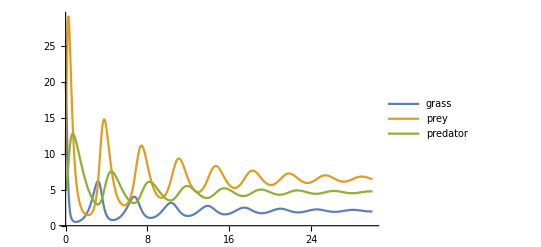

```mathematica
Plot[Evaluate[{x[t], y[t], z[t]}/.sol], {t, 0, 30}, PlotRange->All, PlotLegends->Placed[{"grass", "prey", "predator"}, Top]]
```

```mathematica
Export["mymodel.pdf",%]
```

mymodel.pdf

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["mymodel.pdf"]]]
```